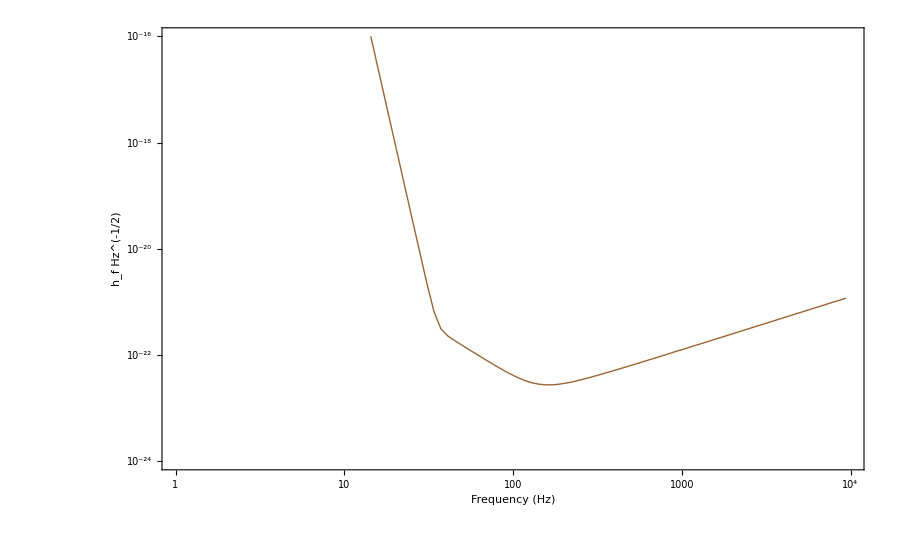

```mathematica
v0=ListLogLogPlot[Import["D:\\oldligo.txt","Table"],PlotRange->{{1,10^4},{10^-24,10^-16}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,4}],Table[{10^i,Superscript[10,i]},{i,-24,-16}]},Joined->True,PlotStyle->{{Thickness[Large],Brown}},FrameLabel->{"Frequency (Hz)",(Subscript[Style["h",30],Style["f",22]] )(Subsuperscript["  Hz","","-1/2"] )},BaseStyle ->{FontFamily->"Arial",18},ImageSize->900,Frame->True]
```

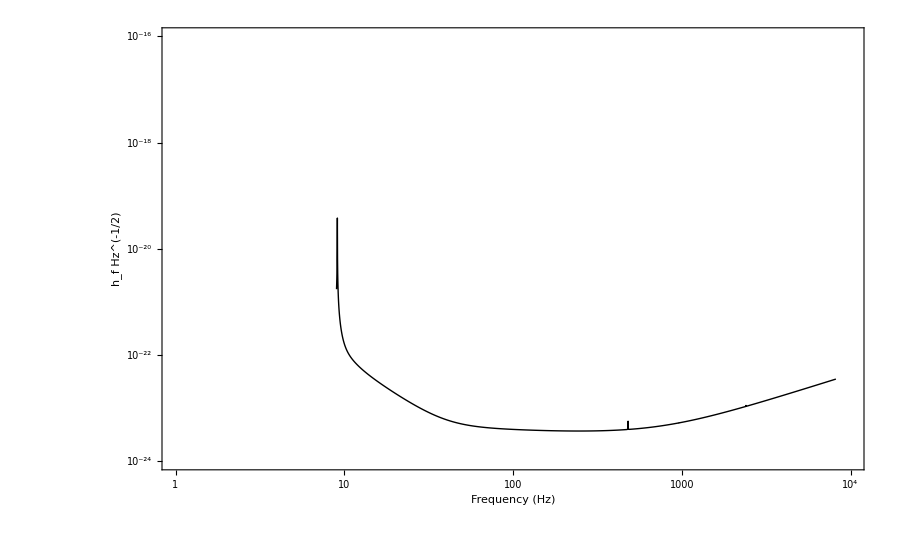

```mathematica
v1=ListLogLogPlot[Import["D:\\aligo.txt","Table"],PlotRange->{{1,10^4},{10^-24,10^-16}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,4}],Table[{10^i,Superscript[10,i]},{i,-24,-16}]},Joined->True,PlotStyle->{{Thickness[Large],Black}},FrameLabel->{"Frequency (Hz)", (Subscript[Style["h",30],Style["f",22]] )(Subsuperscript["  Hz","","-1/2"] )},BaseStyle ->{FontFamily->"Arial",18},ImageSize->900,Frame->True]
```

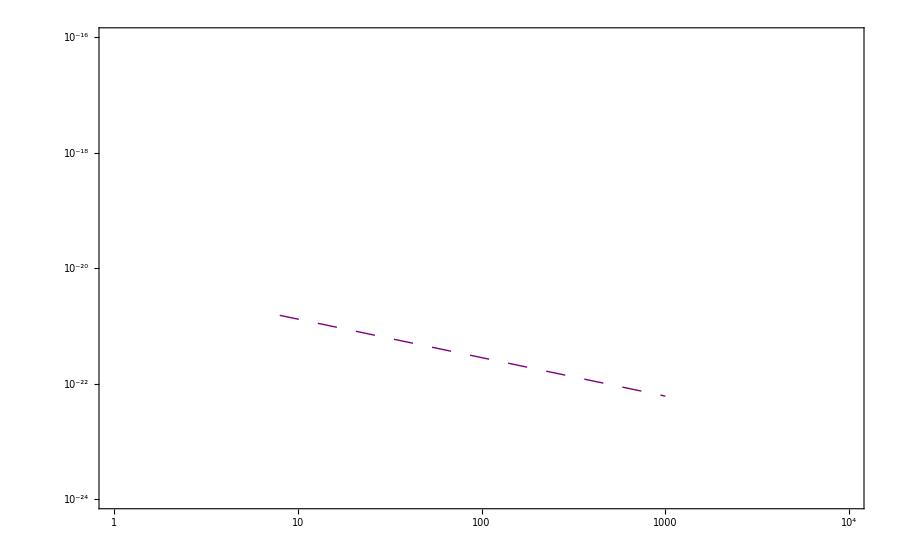

```mathematica
ClearAll[m1,m2 , mchirp,M,r,d,Amplitu]
d=r*1.0292712503*10^8;
r=410*10^6;
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
Amplitu[m1_,m2_,f_]= (mchirp[m1,m2]*4.92549095*10^-6)^(5/6)*d^(-1)*(3.14)^(-2/3)*(5/6)^(1/2)*f^(-2/3);

Needs["PlotLegends`"]
v2=LogLogPlot[{Amplitu[36,29,f]},{f,8,1000},PlotStyle->{{Dashing[Large],Thickness[Large],Purple}},PlotRange->{{1,10^4},{10^-24,10^-16}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,4}],Table[{10^i,Superscript[10,i]},{i,-24,-19}]}FrameLabel->{"Frequency (Hz)",(Subscript[Style["h",30],Style["f",22]] )(Subsuperscript["  Hz","","-1/2"] )},BaseStyle ->{FontFamily->"Arial",18},ImageSize->900,Frame->True]
```

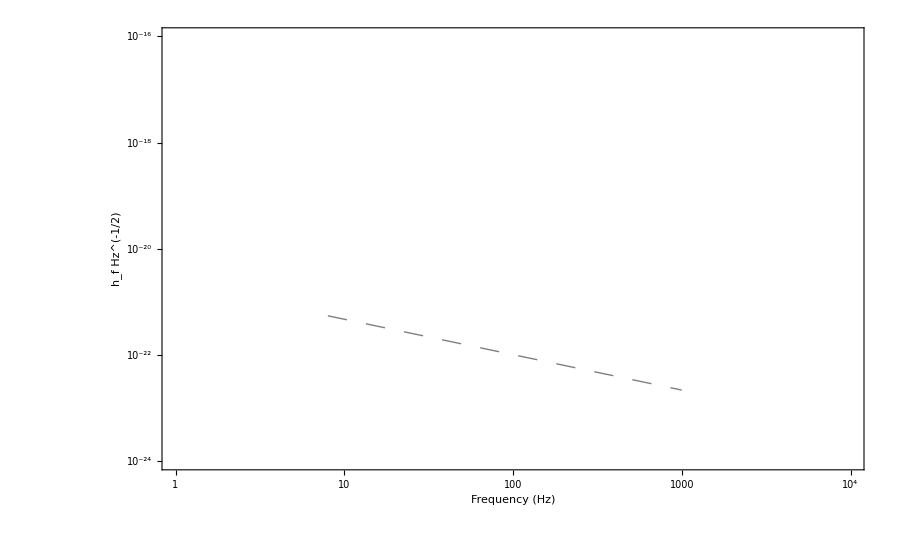

```mathematica
ClearAll[m1,m2 , mchirp,M,r,d,Amplitu]
d=r*1.0292712503*10^8;
r=440*10^6;
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
Amplitu[m1_,m2_,f_]= (mchirp[m1,m2]*4.92549095*10^-6)^(5/6)*d^(-1)*(3.14)^(-2/3)*(5/6)^(1/2)*f^(-2/3);

Needs["PlotLegends`"]
v3=LogLogPlot[{Amplitu[14.2,7.5,f]},{f,8,1000},PlotStyle->{{Dashing[Large],Thickness[Large],Gray}},PlotRange->{{1,10^4},{10^-24,10^-16}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,4}],Table[{10^i,Superscript[10,i]},{i,-24,-19}]},FrameLabel->{"Frequency (Hz)",(Subscript[Style["h",30],Style["f",22]] )(Subsuperscript["  Hz","","-1/2"] )},BaseStyle ->{FontFamily->"Arial",18},ImageSize->900,Frame->True]
```

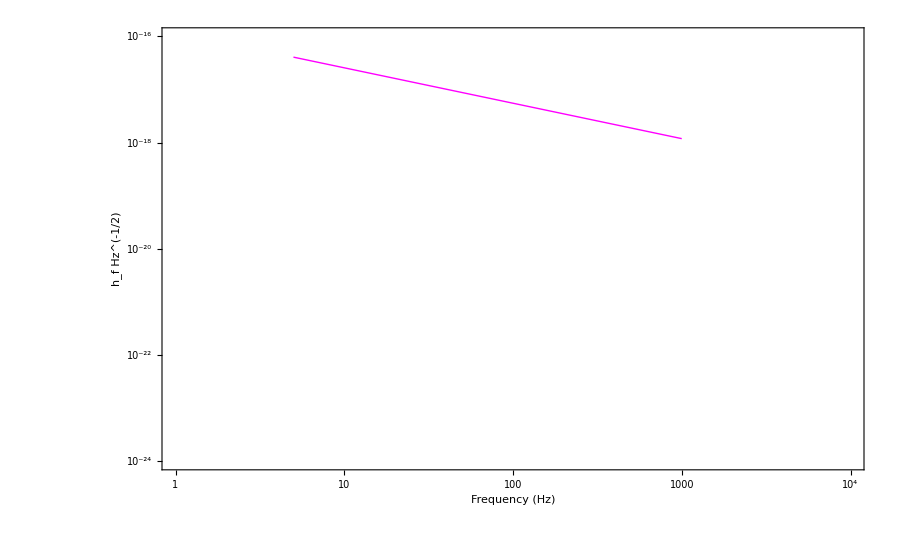

```mathematica
ClearAll[m1,m2 , mchirp,M,r,d,Amplitu]
d=r*1.0292712503*10^8;
r=8*10^3;
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
Amplitu[m1_,m2_,f_]= (mchirp[m1,m2]*4.92549095*10^-6)^(5/6)*d^(-1)*(3.14)^(-2/3)*(5/6)^(1/2)*f^(-2/3);

Needs["PlotLegends`"]
v4=LogLogPlot[{Amplitu[10,10,f]},{f,5,1000},PlotStyle->{{Thickness[Large],Magenta}},PlotRange->{{1,10^4},{10^-24,10^-16}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,4}],Table[{10^i,Superscript[10,i]},{i,-24,-16}]},FrameLabel->{"Frequency (Hz)",(Subscript[Style["h",30],Style["f",22]] )(Subsuperscript["  Hz","","-1/2"] )},BaseStyle ->{FontFamily->"Arial",18},ImageSize->900,Frame->True]
```

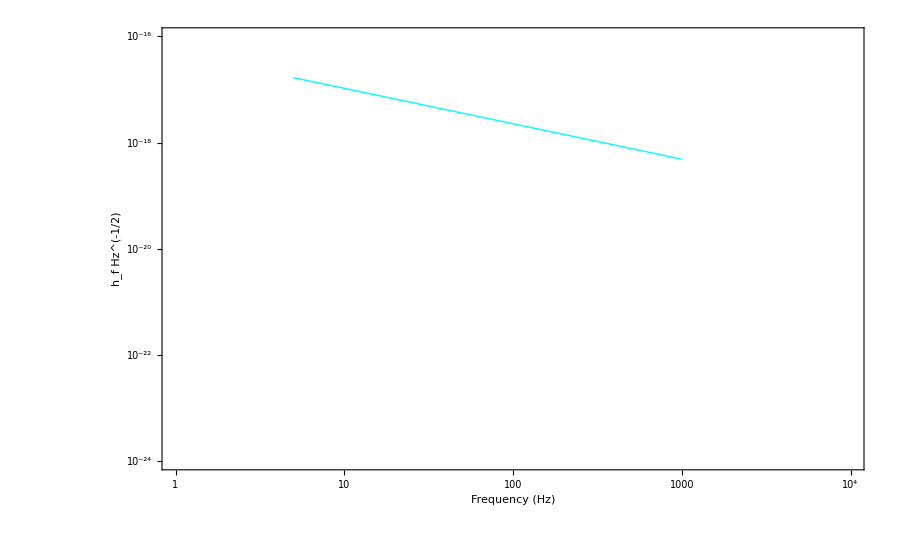

```mathematica
ClearAll[m1,m2 , mchirp,M,r,d,Amplitu]
d=r*1.0292712503*10^8;
r=8*10^3;
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
Amplitu[m1_,m2_,f_]= (mchirp[m1,m2]*4.92549095*10^-6)^(5/6)*d^(-1)*(3.14)^(-2/3)*(5/6)^(1/2)*f^(-2/3);

Needs["PlotLegends`"]
v5=LogLogPlot[{Amplitu[10,1.4,f]},{f,5,1000},PlotStyle->{Thickness[Large],Cyan},PlotRange->{{1,10^4},{10^-24,10^-16}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,4}],Table[{10^i,Superscript[10,i]},{i,-24,-16}]},FrameLabel->{"Frequency (Hz)",(Subscript[Style["h",30],Style["f",22]] )(Subsuperscript["  Hz","","-1/2"] )},BaseStyle ->{FontFamily->"Arial",18},ImageSize->900,Frame->True]
```

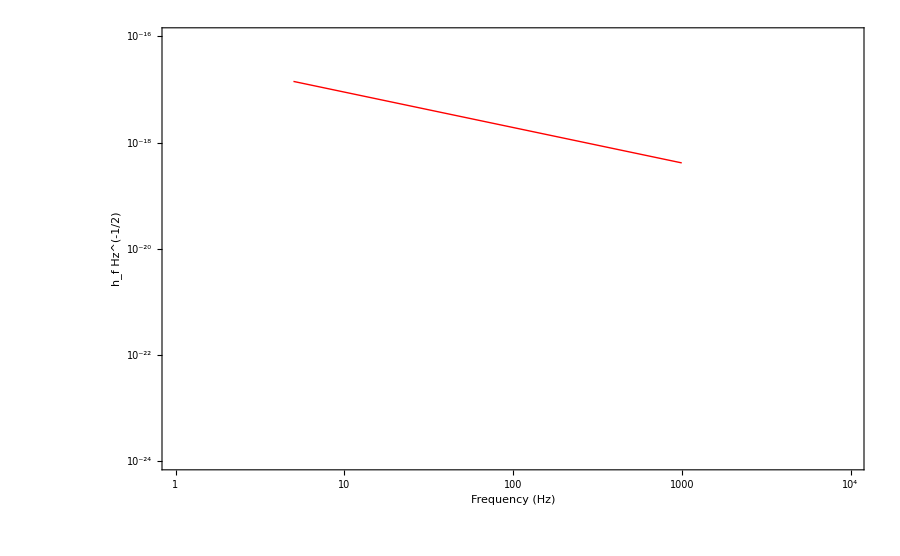

```mathematica
ClearAll[m1,m2 , mchirp,M,r,d,Amplitu]
d=r*1.0292712503*10^8;
r=8*10^3;
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
Amplitu[m1_,m2_,f_]= (mchirp[m1,m2]*4.92549095*10^-6)^(5/6)*d^(-1)*(3.14)^(-2/3)*(5/6)^(1/2)*f^(-2/3);

Needs["PlotLegends`"]
v6=LogLogPlot[{Amplitu[10,1,f]},{f,5,1000},PlotStyle->{Thickness[Large],Red},PlotRange->{{1,10^4},{10^-24,10^-16}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,4}],Table[{10^i,Superscript[10,i]},{i,-24,-16}]},FrameLabel->{"Frequency (Hz)",(Subscript[Style["h",30],Style["f",22]] )(Subsuperscript["  Hz","","-1/2"] )},BaseStyle ->{FontFamily->"Arial",18},ImageSize->900,Frame->True]
```

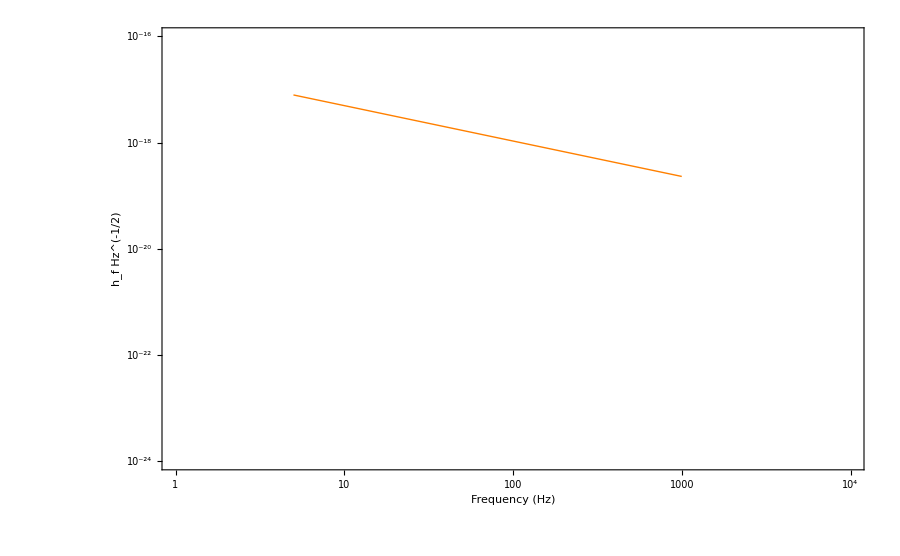

```mathematica
ClearAll[m1,m2 , mchirp,M,r,d,Amplitu]
d=r*1.0292712503*10^8;
r=8*10^3;
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
Amplitu[m1_,m2_,f_]= (mchirp[m1,m2]*4.92549095*10^-6)^(5/6)*d^(-1)*(3.14)^(-2/3)*(5/6)^(1/2)*f^(-2/3);
Needs["PlotLegends`"]
v7=LogLogPlot[{Amplitu[1.4,1.4,f]},{f,5,1000},PlotStyle->{Thickness[Large],Orange},PlotRange->{{1,10^4},{10^-24,10^-16}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,4}],Table[{10^i,Superscript[10,i]},{i,-24,-16}]},FrameLabel->{"Frequency (Hz)",(Subscript[Style["h",30],Style["f",22]] )(Subsuperscript["  Hz","","-1/2"] )},BaseStyle ->{FontFamily->"Arial",18},ImageSize->900,Frame->True]
```

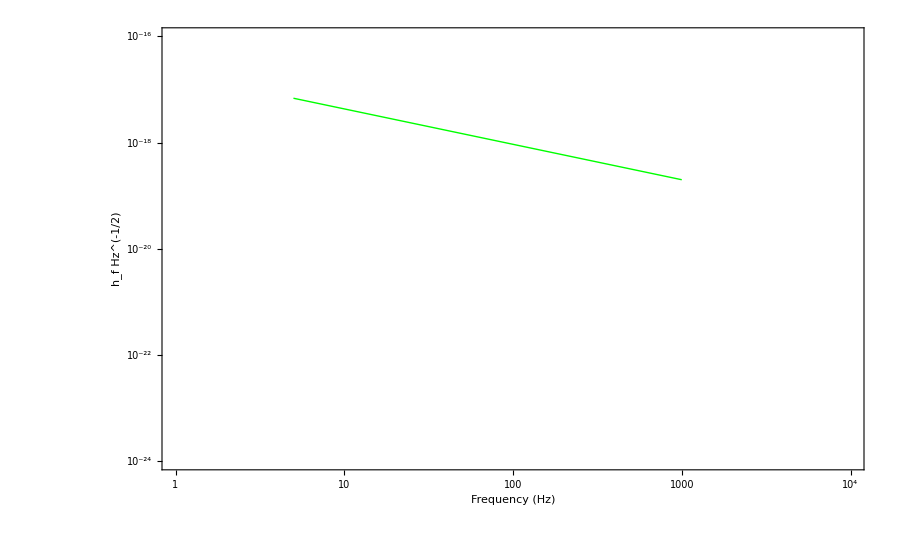

```mathematica
ClearAll[m1,m2 , mchirp,M,r,d,Amplitu]
d=r*1.0292712503*10^8;
r=8*10^3;
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
Amplitu[m1_,m2_,f_]= (mchirp[m1,m2]*4.92549095*10^-6)^(5/6)*d^(-1)*(3.14)^(-2/3)*(5/6)^(1/2)*f^(-2/3);

Needs["PlotLegends`"]
v8=LogLogPlot[{Amplitu[1.4,1,f]},{f,5,1000},PlotStyle->{Thickness[Large],Green},PlotRange->{{1,10^4},{10^-24,10^-16}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,4}],Table[{10^i,Superscript[10,i]},{i,-24,-16}]},FrameLabel->{"Frequency (Hz)",(Subscript[Style["h",30],Style["f",22]] )(Subsuperscript["  Hz","","-1/2"] )},BaseStyle ->{FontFamily->"Arial",18},ImageSize->900,Frame->True]
```

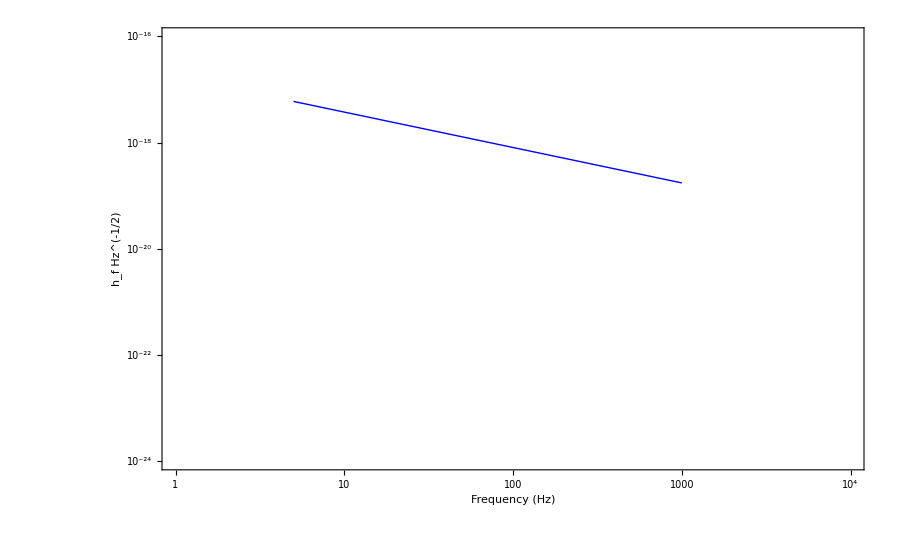

```mathematica
ClearAll[m1,m2 , mchirp,M,r,d,Amplitu]
d=r*1.0292712503*10^8;
r=8*10^3;
mchirp[m1_,m2_]=(m1 m2)^(3/5) (m1+m2)^(-1/5);
Amplitu[m1_,m2_,f_]= (mchirp[m1,m2]*4.92549095*10^-6)^(5/6)*d^(-1)*(3.14)^(-2/3)*(5/6)^(1/2)*f^(-2/3);

Needs["PlotLegends`"]
v9=LogLogPlot[{Amplitu[1,1,f]},{f,5,1000},PlotStyle->{Thickness[Large],Blue},PlotRange->{{1,10^4},{10^-24,10^-16}},Ticks->{Table[{10^i,Superscript[10,i]},{i,0,4}],Table[{10^i,Superscript[10,i]},{i,-24,-16}]},FrameLabel->{"Frequency (Hz)",(Subscript[Style["h",30],Style["f",22]] )(Subsuperscript["  Hz","","-1/2"] )},BaseStyle ->{FontFamily->"Arial",18},ImageSize->900,Frame->True]
```

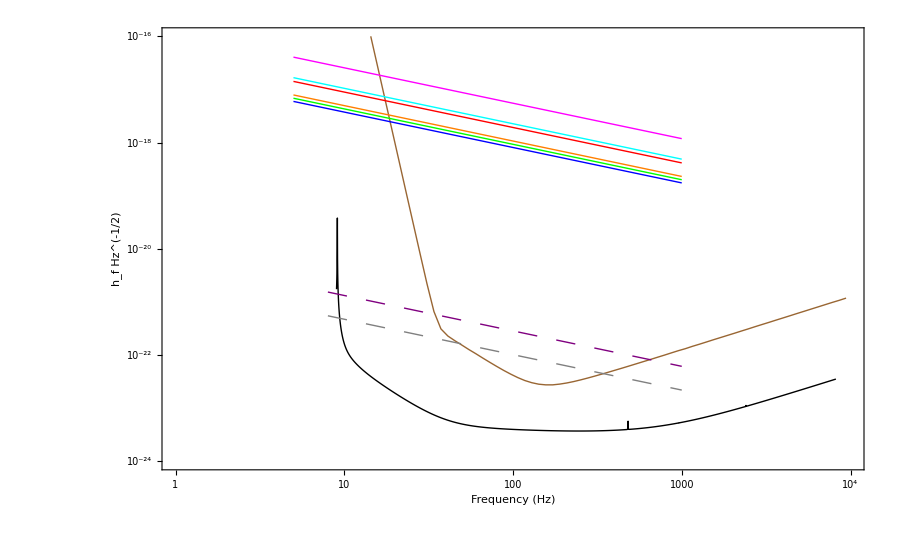

```mathematica
Show[v0,v1,v2,v3,v4,v5,v6,v7,v8,v9]
```

```mathematica
Needs["PlotLegends`"]

ShowLegend[Show[v0,v1,v2,v3,v4,v5,v6,v7,v8,v9],
{{{Graphics[{Brown,Thickness[Large],Line[{{0,0},{4,0}}]}],Style["LIGO sensitivity",Bold,13]},{Graphics[{Black,Thickness[Large],Line[{{0,0},{4,0}}]}],Style["aLIGO sensitivity",Bold,13]},{Graphics[{Purple,Dashing[Medium],Thickness[Large],Line[{{0,0},{4,0}}]}],Style["GW150914",Bold,13]},{Graphics[{Gray,Dashing[Medium],Thickness[Large],Line[{{0,0},{4,0}}]}],Style["GW151226",Bold,13]},{Graphics[{Magenta,Thickness[Large],Line[{{0,0},{4,0}}]}],Style["BH-BH",Bold,13]},{Graphics[{Cyan,Thickness[Large],Line[{{0,0},{4,0}}]}],Style["BH-NS",Bold,13]},{Graphics[{Red,Thickness[Large],Line[{{0,0},{4,0}}]}],Style["BH-WD",Bold,13]},
{Graphics[{Orange,Thickness[Large],Line[{{0,0},{4,0}}]}],Style["NS-NS",Bold,13]},{Graphics[{Green,Thickness[Large],Line[{{0,0},{4,0}}]}],Style["NS-WD",Bold,13]},{Graphics[{Blue,Thickness[Large],Line[{{0,0},{4,0}}]}],Style["WD-WD",Bold,13]}},LegendSize->{0.50,0.75},LegendPosition->{0.95,-0.2},LegendShadow->None}]
```

-Graphics-